```mathematica
F[n_]:=(-1/2*(Z^2 Subscript[m, p])/(n^2 (Subscript[m, e]+Subscript[m, p]))*(Subscript[m, e]/ℏ^2)*(e^2/(4*Pi*Subscript[ϵ, 0])^2))*e
```

```mathematica
Needs["PhysicalConstants`"]
```

```mathematica
Subscript[m, p]:=1.672621777*10^(-27)
```

```mathematica
Subscript[m, e]:=9.10938291*10^(-31)
ℏ:=1.054571726*10^(-34)
Subscript[ϵ, 0]:=8.854187817*10^(-12)
e:=1.602176565*10^(-19)
```

```mathematica
F[n]
```

-54.3931/n^2

```mathematica
Z:=2
```

```mathematica
F[1]
```

-54.3931

```mathematica
NumberForm[F[1],{10,6}]
```

-54.393147

```mathematica
NumberForm[F[2],{10,6}]
```

-13.598287

```mathematica
NumberForm[F[3],{10,6}]
```

-6.043683

```mathematica
G[n_]:=(F[n]-F[1])/(1.24*10^(-4))
```

```mathematica
G[1]
```

0.

```mathematica
G[2]
```

328991.

```mathematica
G[3]
```

389915.

```mathematica
list:={0,329179.76197, 390140.964175}
```

```mathematica
frac[n_]:=Abs[G[n]-Part[list,n]]/Part[list,n]
```

```mathematica
frac[1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Indeterminate

```mathematica
frac[2]
```

0.000574019

```mathematica
frac[3]
```

0.000579109

```mathematica
Part[list,3]-Part[list,2]
```

60961.2

```mathematica
1/Out[60]*10^7
```

164.039

```mathematica
(* Problem 2*)
(* a *)
```

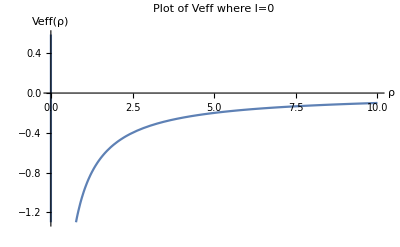

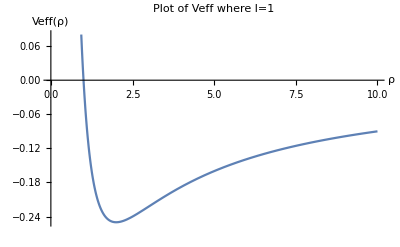

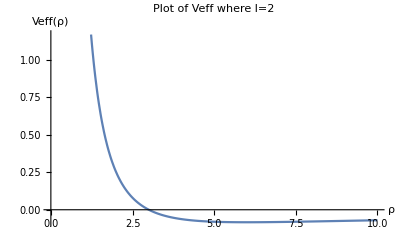

```mathematica
Veff[ρ_]:=-1/ρ+(l*(l+1))/(2*ρ^2)
Do[l:=n;Plot[Veff[ρ],{ρ,-0.01,10},AxesLabel->{"ρ","Veff(ρ)"},PlotLabel->"Plot of Veff where l="<>ToString[l]]//Print,{n,0,2}]
```

```mathematica
l:=2
ϵ:=-0.05556
ep:=$MachineEpsilon 
NDSolve[{-u''[ρ]/2+(Veff[ρ]-ϵ)*u[ρ]==0,u[ep]==0,u'[ep]==2},u,{ρ,ep,30} ]
Plot[u[ρ]/.%,{ρ,ep,30},AxesLabel->{"ρ","u[ρ]"},PlotLabel->"Plot of u[ρ] when l="<>ToString[l]<>" and ϵ="<>ToString[ϵ]]
```

{{u→                                  -16
InterpolatingFunction[{{2.22045 10   , 30.}}, <>]}}

-Graphics-

```mathematica
a:=0.529*10^(-10)
PlanckConstantReduced
```

1.05457×10^-34 Joule Second

```mathematica
Energy[x_]:=(PlanckConstantReduced^2*x)/(ElectronMass*a^2)
```

```mathematica
Energy[-0.125]
```

-(5.45333×10^-19 Joule^2 Second^2)/Kilogram

```mathematica
(* Problem 3*)
```

```mathematica
U[n_,l_,m_,r_,t_,phi_]:=2 Sqrt[(2/(n*a))^3 ((n-l-1)!/(2 n (n+l)!))]*3 Exp[-r/(n a)]*(2 r/(n a))^l*4 LaguerreL[n-l-1,2 l+1,2 r/(n a)]*5 SphericalHarmonicY[l,m,t,phi]
```

```mathematica
s[n_,l_,m_,n1_,l1_,m1_]:=Integrate[Conjugate[U[n,l,m,r,t,phi]]*z*U[n1,l1,m1,r,t,phi]*r^2*Sin[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}]
```

```mathematica
s[2,0,0,1,0,0]
```

z ∫_0^∞ ∫_0^π ∫_0^(2 π) r^2 Conjugate[U[2,0,0,r,t,phi]] Sin[t] U[1,0,0,r,t,phi]ⅆphiⅆtⅆr

```mathematica
Clear[a]
```

```mathematica
R20:=1/Sqrt[2]*a^(-3/2)(1-0.5*r/a)*Exp[-r/(2*a)]
```

```mathematica
R21:=1/Sqrt[24]*a^(-3/2)*(r/a)*Exp[-r/(2*a)]
```

```mathematica
R30:=2/Sqrt[27]*a^(-3/2)*(1-(2/3)*(r/a)+(2/27)*(r/a)^2)*Exp[-r/(3*a)]
```

```mathematica
R10:=2*a^(-3/2)*Exp[-r/a]
```

```mathematica
R31:=8/(27*Sqrt[6])*a^(-3/2)*(1-(1/6)*(r/a))*(r/a)*Exp[-r/(3*a)]
R32:=4/(81*Sqrt[30])*a^(-3/2)*(r/a)^2*Exp[-r/(3*a)]
```

```mathematica
Integrate[r*Cos[t]*R20*Conjugate[SphericalHarmonicY[0,0,t,phi]]*R10*SphericalHarmonicY[0,0,t,phi]*r^2*Sin[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}]
```

0

```mathematica
Integrate[r*Cos[t]*R21*Conjugate[SphericalHarmonicY[1,0,t,phi]]*R10*SphericalHarmonicY[0,0,t,phi],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}]
```

Integrate::idiv: Integral of r does not converge on {0, ∞}.

∫_0^∞ 1/4 √3 π r R10 R21ⅆr

```mathematica
Integrate[r*Cos[t]*R30*Conjugate[SphericalHarmonicY[0,0,t,phi]]*R10*SphericalHarmonicY[0,0,t,phi]*r^2*Sin[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}]
```

0

```mathematica
Integrate[r*Cos[t]*R31*Conjugate[SphericalHarmonicY[1,0,t,phi]]*R10*SphericalHarmonicY[0,0,t,phi],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}]
```

Integrate::idiv: Integral of r does not converge on {0, ∞}.

∫_0^∞ 1/4 √3 π r R10 R31ⅆr

```mathematica
Integrate[z*R32*Conjugate[SphericalHarmonicY[2,0,t,phi]]*R10*SphericalHarmonicY[0,0,t,phi]*r^2*Sin[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}]
```

0

```mathematica
Simplify[Integrate[r*Cos[t]*Conjugate[(1/Sqrt[24]*a^(-3/2)*(r/a)*Exp[-r/(2*a)])*SphericalHarmonicY[1,0,t,phi]]*(1/Sqrt[2]*a^(-3/2)(1-0.5*r/a)*Exp[-r/(2*a)])*SphericalHarmonicY[0,0,t,phi]*r^2*Sin[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a ∈Reals&&a>0]
```

-3. a

```mathematica
U[n_,l_,m_,r_,t_,phi_]:=Sqrt[(2/(n a))^3 ((n-l-1)!/(2 n (n+l)!))]*Exp[-r/(n a)]*(2 r/(n a))^l*LaguerreL[n-l-1,2 l+1,2 r/(n a)]*SphericalHarmonicY[l,m,t,phi]
```

```mathematica
Simplify[Integrate[Conjugate[U[2,0,0,r,t,phi]]*U[1,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]
```

0

```mathematica
Simplify[Integrate[Conjugate[U[2,1,0,r,t,phi]]*U[1,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]
```

(128 √2 a)/243

```mathematica
Simplify[Integrate[Conjugate[U[3,0,0,r,t,phi]]*U[1,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]
```

0

```mathematica
Simplify[Integrate[Conjugate[U[3,1,0,r,t,phi]]*U[1,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]
```

(27 a)/(64 √2)

```mathematica
Simplify[Integrate[Conjugate[U[3,2,0,r,t,phi]]*U[1,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]
```

0

```mathematica
Simplify[Integrate[Conjugate[U[2,1,0,r,t,phi]]*U[2,0,0,r,t,phi]*r^3*Sin[t]*Cos[t],{r,0,Infinity},{t,0,Pi},{phi,0,2*Pi}],a∈Reals && a>0]
```

-3 a

```mathematica
sx:=ℏ/2* {{0,1},{1,0}} //MatrixForm
sy:=ℏ/2*{{0,-ⅈ},{ⅈ,0}} //MatrixForm
sz:=ℏ/2*{{1,0},{0,-1}} //MatrixForm
```

```mathematica
sx
sy
sz
```

(0 | ℏ/2
ℏ/2 | 0)

(0 | -(ⅈ ℏ)/2
(ⅈ ℏ)/2 | 0)

(ℏ/2 | 0
0 | -ℏ/2)

```mathematica
sx*Sin[θ]*Cos[ϕ]+sy*Sin[θ]*Sin[ϕ]+sz*Cos[θ]//MatrixForm
```

Cos[θ] (ℏ/2 | 0
0 | -ℏ/2)+Cos[ϕ] (0 | ℏ/2
ℏ/2 | 0) Sin[θ]+(0 | -(ⅈ ℏ)/2
(ⅈ ℏ)/2 | 0) Sin[θ] Sin[ϕ]

```mathematica
Simplify[sx*Sin[θ]]
```

(0 | ℏ/2
ℏ/2 | 0) Sin[θ]

```mathematica
Eigensystem[Cos[θ] ({{ℏ/2, 0}, {0, -ℏ/2}})+Cos[ϕ] ({{0, ℏ/2}, {ℏ/2, 0}}) Sin[θ]+({{0, -(ⅈ ℏ)/2}, {(ⅈ ℏ)/2, 0}}) Sin[θ] Sin[ϕ]]
```

{{-ℏ/2,ℏ/2},{{-(Cos[ϕ] Sin[θ]-ⅈ Sin[θ] Sin[ϕ])/(1+Cos[θ]),1},{-(Cos[ϕ] Sin[θ]-ⅈ Sin[θ] Sin[ϕ])/(-1+Cos[θ]),1}}}

```mathematica
TeXForm[{-(Cos[ϕ] Sin[θ]-ⅈ Sin[θ] Sin[ϕ])/(1+Cos[θ]),1}//MatrixForm]
```

\left(
\begin{array}{c}
 -\frac{\sin (\theta ) \cos (\phi )-i \sin (\theta ) \sin (\phi )}{\cos (\theta
   )+1} \\
 1 \\
\end{array}
\right)

```mathematica
TeXForm[{-(Cos[ϕ] Sin[θ]-ⅈ Sin[θ] Sin[ϕ])/(-1+Cos[θ]),1}//MatrixForm]
```

\left(
\begin{array}{c}
 -\frac{\sin (\theta ) \cos (\phi )-i \sin (\theta ) \sin (\phi )}{\cos (\theta
   )-1} \\
 1 \\
\end{array}
\right)